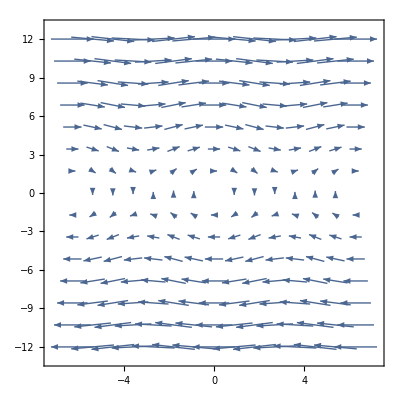

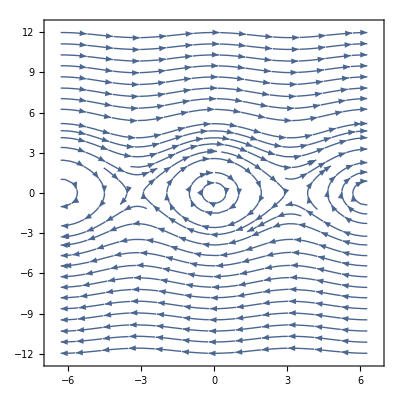

```mathematica
m =1;
MOI =0.25;
d = 1;
g=9.81;
vec[p_,th_]:={p/MOI,-m g d Sin[th]}
VectorPlot[vec[p,th],{th,-2Pi,2Pi},{p,-12,12}]
StreamPlot[vec[p,th],{th,-2Pi,2Pi},{p,-12,12}]
```

```mathematica
vec[p,th]
```

{-9.81 Sin[th],p}